## Assignment 7

due the week after thanksgiving break

3.1.4

(4) Waves in shallow water:  Waves on the surface of water with long wavelength compared to the water depth are also described by the wave equation. In this problem you will derive the equation from first principles using the following method, analogous to that for a wave on a string. During the wave motion, a mass of fluid in an element of unit width into the paper, equilibrium height h and length Δx moves a distance η and assumes a new height h+z(x,t) and a length (1+ ∂η/∂x)Δx, but remains of unit width into the paper. (See Fig. 3.7.)

Fig. 3.7. A wave in shallow water, with motion greatly exaggerated.

(a) Using the incompressibility of the fluid (the volume of the element remains fixed during its motion) show that, to lowest approximation,

z=-h∂η/∂x.

(b) Neglecting surface tension, the net force in the x-direction on the element face of height h+z arises from the difference in hydrostatic pressure on each face of the element due to elements on the right and left of different heights. The hydrostatic pressure is a function of distance y from the bottom: p = ℳ g (h+z(x,t)-y), where ℳ is the mass density of the water and g is the acceleration of gravity. Show that the net force in the x-direction, ΔF_x, is given by

ΔF_x=-ℳ g h (∂z)/(∂x)Δx.

(c) Using the results from part (a) and (b), and Newton's 2nd law for the mass element,  show that shallow water waves satisfy the wave equation (∂^2 η)/(∂t^2)=c^2(∂^2 η)/(∂x^2), or alternately,

(∂^2 z)/(∂t^2)=c^2(∂^2 z)/(∂x^2).

where the wave speed c is given by

c=√(g h)

(d) A typical ocean depth is on the order of 4 km. Tidal waves have wavelengths that are considerably larger than this, and are therefore well described by the shallow-water wave equation. Calculate the wave speed (in kilometers per hour) for a tidal wave.

### Solution

#### Solution to (a)

By incompressibility, the volume ⅆV of an element does not change during its motion. Initially, this volume is ⅆV = h Δx (times the depth into the page, taken to be unity). According to the figure, after a displacement η(x,t) the volume is ⅆV =(h+z(x,t) )(1+ ∂η/∂x)Δx. Since nothing has changed (h+z(x,t) )(1+ ∂η/∂x)Δx=h Δx. Solving, we obtain z=-h∂η/∂x.

#### Solution to (b)

Since the height of the water is different on each side of the element, there is a net pressure force on the element that causes it to move to the left or right. The net force on the left side of an element, at position x, is F_left=∫_0^(h+z) ⅆy p (y)= ℳ g ∫_0^(h+z) ⅆy (h+z(x,t)-y). The net force on the rhs of the element, at x+Δx, isF_right=-ℳ g ∫_0^(h+z(x+Δx,t)) ⅆy (h+z(x+Δx,t)-y). Adding these yields
ΔF_x=ℳ g ∫_0^(h+z) ⅆy (z(x,t)-z(x+Δx,t))+ℳ g (∫ⅆy)_(h+z(x,t))^(h+z(x+Δx,t))(h-y+z(x+Δx,t)). Dropping nonlineat terms in z. amnd Taylor expanding z(x+Δx), the first integral yields -ℳ g h Δx∂z/∂x, and the second integral yields -ℳ g z  Δx ∂z/∂x, which is nonlinear and so can also be dropped.

#### Solution to (c)

According to Newton, mass times acceleration in the x direction equals net force, so 
ℳ Δx (∂^2 η)/(∂t^2) = ΔF_x=-ℳ g h Δx∂z/∂x . But,  from (a), z=-h∂η/∂x, so
(∂^2 η)/(∂t^2)= g  ∂/(∂x) h ∂/(∂x)η(x,t).

#### Solution to (d)

```mathematica
Clear["Global`*"]
```

```mathematica
g = 9.8;
h=4000;
```

```mathematica
c= Sqrt[g h]
```

197.99

This is in m/sec. In km/hr:

```mathematica
c = c 3600/1000
```

712.764

Tidal waves move FAST.

3.1.5

(5) In this problem we consider shallow-water waves, sloshing in the x-direction in a long channel of width L in the x-direction.  Boundary conditions on the waves  are that the horizontal fluid displacement in the x-direction, η (defined in the previous problem), equals zero at the channel boundaries (at x=0 and x=L).

(a) Find the eigenmodes and eigenfrequencies for η(x,t).

(b) Plot the wave height z vs x for the first three sloshing modes.

### Solution

#### (a)

Spearation of variables on  wave equation for η(x,t) = f(t)ψ(x) implies that f''(t)=-ω^2f(t) and ψ''(x) = -ω^2/c^2ψ(x) with boundary conditions that ψ(0)=ψ(L)=0 due to the walls. So the solution is our usual sin functions,

		ψ(x) = sin (n π x/L), n=1,2,3,..., 

and corresponding frequencies ω=n π c/L.

#### (b)

Waver height z is related to η according to z=-h∂η/∂x, so if ψ(x) = sin (n π x/L) then
z(x) = - n π h/L cos(n π x/L). Here's a plot of the water height versus position first three modes, neglecting overall amplitude factors::

```mathematica
L=1;
```

```mathematica
z[n_,x_] = Cos[n Pi x/L];
```

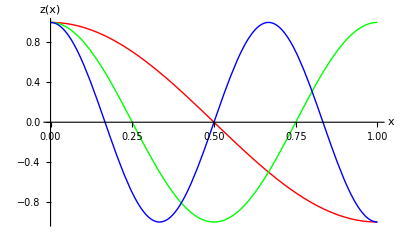

```mathematica
Plot[{z[1,x],z[2,x],z[3,x]},{x,0,L},PlotStyle->{Red,Green,Blue},AxesLabel->{"x","z(x)"}]
```

3.1.7 (a)

(7) Using separation of variables, find the solution for the motion of a string that is governed by the following wave equation:

∂^2/(∂t^2)y(x,t)=∂^2/(∂x^2)y(x,t)+ f(x),

with boundary conditions y(0,t)=0=y(π,t), and initial conditions

(a) y(x,0)=x(π-x),   ∂/(∂t)y(x,0)=0. Take f(x)=0.

### Solution

The general solution for the wave equation is y(x,t)=∑_n (A_n cos ω_n t + B_n sin ω_n t) ψ_n(x) where by separation of variables ψ_n(x) satisfies the eigenvalue problem ψ''(x)=-(ω_n)^2ψ(x)  with boundary conditions ψ_n(0)=ψ_n(π)=0. This implies that ψ_n(x)=sin n x and ω_n=n. Matching to the initial conditions implies B_n=0 and A_n=2/π∫_0^π ⅆx x(π-x)sin n x

```mathematica
A[n_] = Integrate[Sin[n x] x(Pi-x),{x,0,Pi}]2/Pi
```

(2 (2-2 Cos[n π]-n π Sin[n π]))/(n^3 π)

```mathematica
A[n_] = Simplify[%,n∈Integers]
```

-(4 (-1+(-1)^n))/(n^3 π)

No need to make an animatioon but I’ll do it anyway for fun:

```mathematica
ψ[n_,x_] = Sin[n x];
ω[n_] = n;
```

```mathematica
y[x_,t_] = Sum[A[n] Cos[ω[n] t] ψ[n,x],{n,1,10}];
```

```mathematica
ListAnimate[Table[Plot[y[x,t],{x,0,Pi},PlotRange->{-3,3},],{t,0,1.9Pi,.1Pi}]]
```

3.1.18

(18) A cold steak, initially at uniform temperature T(x,0)=8 °C, and of thickness L= 3 cm, is placed on a griddle (at x=0) at temperature T=250 °C. The steak will be cooked medium rare when its minimum internal temperature reaches T=65 °C.  How long does this take? Animate the solution for T(x,t) up to this time. (The boundary condition on the upper face of the meat at x=L can be taken to be approximately insulating. The thermal diffusivity of meat is about 3×10^-7 m^2/s. )

### Solution

The heat equation is

(∂T(x,t))/(∂t)=χ (∂^2 T(x,t))/(∂x^2),

with initial condition T(x,0) =  8, boundary condition T(0,t) = 250,   ∂T/∂x|_(x=L)=0. 
Write
		T(x,t) =T_eq(x) + Σ f_n(t) ψ_n(x) 
where T_eq(x) = 250, 

and by  separation of variables, f_n''(t)=-λ_n f_n, and χ (∂^2 ψ_n(x))/(∂x^2)=-λ_n ψ_n(x). 

Therefore,
		f_n(t)= A_n ⅇ^-λ_nt.

 The general solution for ψ(x) is ψ(x) = A cos √(λ_n/χ)x + B sin √(λ_n/χ)x. Boundary conditions on ψ(x)  are ψ(0)=0, ψ'(L) = 0. Therefore, A=0, ψ(x) = B sin √(λ_n/χ)x, with √(λ_n/χ) determined by  ψ'(L) = 0: cos√(λ_n/χ)L=0. This implies √(λ_n/χ)L = (n+1/2)π, n=0,1,2,3,... So,
 
		T(x,t) = T_eq+ Σ_(n=0,1,2..)A_n ⅇ^-λ_nt sin (n+1/2)π x/L,

 with λ_n = χ[(n +1/2) π/L]^2.
 
  To find A_n, match initial conditions:
 T(0,t) - T_eq =8-250= -242 =Σ_(n=0,1,2..)A_n sin (n+1/2)π x/L . The eigenmodes form an orthogonal set  so

```mathematica
Clear["Global"]
```

```mathematica
L=3/100;
```

(steak thickness in meters.)

```mathematica
A[n_] = (2/L) Integrate[-242 Sin[(n+1/2) Pi x/L],{x,0,L}]
```

-(968 (1+Sin[n π]))/(π+2 n π)

```mathematica
χ = 3 10^-7;
λ[n_] = χ ((n+1/2) Pi/L)^2;
```

```mathematica
T[x_,t_] = 250 + Sum[A[n] ⅇ^(-λ[n] t) Sin[(n+1/2) Pi x/L],{n,0,40}];
```

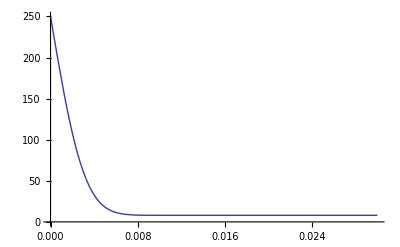
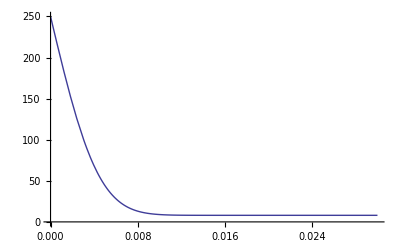
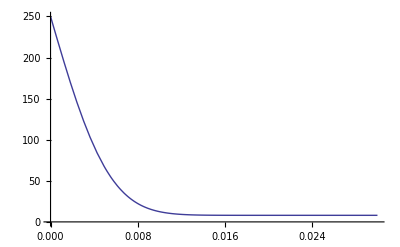
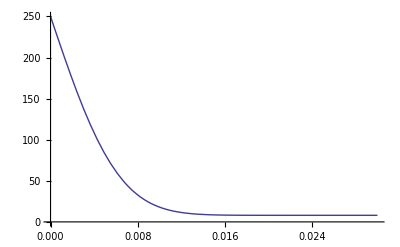
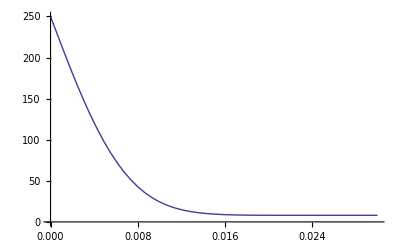
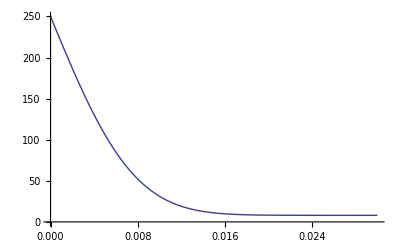
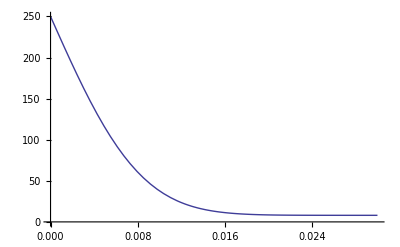
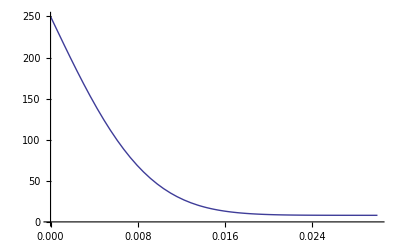

```mathematica
Table[Plot[T[x,t],{x,0,L},PlotRange->{0,250}],{t,10,800,10}]
```

```mathematica
ListAnimate[%]
```

The minimum temperature is at x=L.

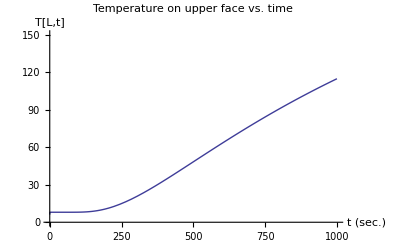

```mathematica
Plot[T[L,t],{t,0,1000},PlotRange->{0,150},PlotLabel->"        Temperature on upper face vs. time",AxesLabel->{"t (sec.)","T[L,t]"}]
```

When does T(L,t) = 65?

```mathematica
FindRoot[T[L,t] ==65, {t,500}]
```

{t→613.068}

It  takes about 10 minutes to cook through on this very hot griddle. (Normally, you would turn it over so the bottom isn't burned.)